```mathematica
??StudentTDistribution
```

StudentTDistribution[ν] represents a Student t distribution with ν degrees of freedom.
StudentTDistribution[μ,σ,ν] represents a Student t distribution with location parameter μ, scale parameter σ, and ν degrees of freedom.

Attributes[StudentTDistribution]={Protected,ReadProtected}

```mathematica
F[x_]:=CDF[StudentTDistribution[16],x]
```

```mathematica
N[2 (1-F[8/3])]
```

0.0168849

```mathematica
A = List[7,-4,18,17,-3,-5,1,10,11,-2];
B = List[-1,12,-1,-3,3,-5,5,2,-11,-1,-3];
```

```mathematica
Mean[A]
```

5

```mathematica
Mean[B]
```

-3/11

```mathematica
Variance[A]
```

688/9

```mathematica
Variance[B]
```

383/11

```mathematica
N[(√19)/(√(1/10+1/11)*√((Variance[A])+(Variance[B])))]
```

0.945777

```mathematica
F[x_]:=CDF[StudentTDistribution[19],x]
```

```mathematica
N[F[1.33]]
```

0.900368

```mathematica
g[x_]:=x - 1 + (1-x/1000)^1000
```

```mathematica
D[g[x],x]
```

1-(1-x/1000)^999

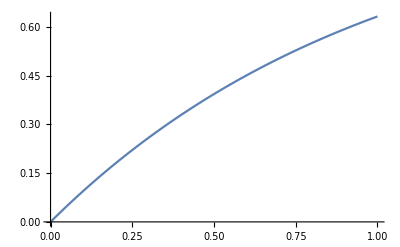

```mathematica
Plot[g'[x],{x,0,1}]
```

```mathematica
g[0]
```

0